## setup

```mathematica
TorqueVectorSphere[{Rx_,Ry_,Rz_},{γx_,γy_,γz_}]:=Graphics3D[{{Specularity[Pink,5],Opacity[0.1],Sphere[]},{Red,Thick,Arrow[{{0,0,0},{Rx,Ry,Rz}}]},{Blue,Thick,Dashed,Line[{{0,0,0},{Rx,Ry,0}}]},
{Blue,Thick,Dashed,Line[{{Rx,Ry,0},{Rx,Ry,Rz}}]},{Green,Thick,Dashed,Line[{{0,0,0},{0,0,Rz}}]},
{Green,Thick,Dashed,Line[{{0,0,Rz},{Rx,Ry,Rz}}]},
{Purple,Thick,Arrow[{{0,0,0},{γx,γy,γz}}]},
Text[Style["Z",20],{0,0,1.3}],Text[Style["X",20],{1.3,0,0}],Text[Style["Y",20],{0,1.3,0}]},Boxed->False,Axes->True,AxesOrigin->{0,0,0},ImageSize->Medium];
```

## one spin, static B

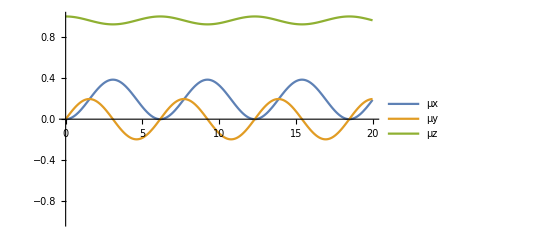

```mathematica
Bz=1;
Bx=0.2;
By=0;
B={Bx,By,Bz};
mu0={0,0,1};
mu={μx[t],μy[t],μz[t]};
muIC=Array[(mu/.t->0)[[#]]==mu0[[#]]&,3];
motionEqs=Thread[D[mu,t]==Cross[mu,B]];
eqs=Flatten@Join[motionEqs,muIC];
tmax=20;
soln=First@NDSolve[eqs,mu,{t,0,tmax}];
{x,y,z}=Array[soln[[#,2]]&,3];
labels={"μx","μy","μz"};
Plot[{x,y,z},{t,0,tmax},PlotRange->{-1,1},PlotLegends->labels]
Manipulate[TorqueVectorSphere[{x,y,z}/.t->τ,{Bx,By,Bz}],{τ,0,tmax,0.001} ]
```

## one spin, oscillating B

```mathematica
(1/2π )10//N
```

15.708

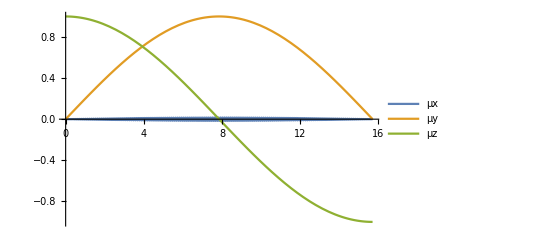

```mathematica
Bz=Cos[2π 10 t];
Bx=0.2;
By=0;
B={Bx,By,Bz};
mu0={0,0,1};
mu={μx[t],μy[t],μz[t]};
muIC=Array[(mu/.t->0)[[#]]==mu0[[#]]&,3];
motionEqs=Thread[D[mu,t]==Cross[mu,B]];
eqs=Flatten@Join[motionEqs,muIC];
tmax=(1/2π )10;
soln=First@NDSolve[eqs,mu,{t,0,tmax}];
{x,y,z}=Array[soln[[#,2]]&,3];
labels={"μx","μy","μz"};
Plot[{x,y,z},{t,0,tmax},PlotRange->{-1,1},PlotLegends->labels]
Manipulate[TorqueVectorSphere[{x,y,z}/.t->τ,B/.t->τ],{τ,0,tmax,0.001} ]
```

## magnetization, oscillating B, relaxation

```mathematica
0.3^2
```

0.09

```mathematica
0.955^2
```

0.912025

Bloch Equations:

Mx'(t)==-By Mz(t)+Bz My(t)-(Mx(t))/T2

My'(t)==Bx Mz(t)-Bz Mx(t)-(Mx(t))/T2

Mz'(t)==-Bx My(t)+By Mx(t)-(Mz(t))/T1

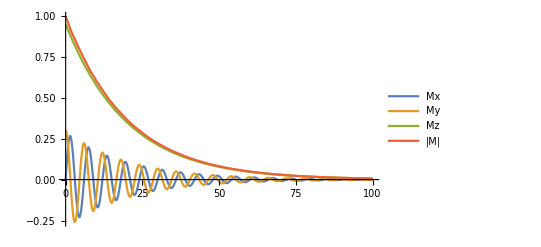

```mathematica
Clear[Bx,By,Bz,T1,T2]
B={Bx,By,Bz};
mag0={0,0.3,0.95};
mag={Mx[t],My[t],Mz[t]};(*magnetization*)
decay={{-1/T2,0,0},{-1/T2,0,0},{0,0,-1/T1}};
magIC=Array[(mag/.t->0)[[#]]==mag0[[#]]&,3];
motionEqs=Thread[D[mag,t]==Cross[mag,B]+Dot[decay,mag]];
"Bloch Equations:"
For[i=1,i<4,i++,
Print[motionEqs[[i]]//TraditionalForm]
]
Bz=1;
Bx=0*Cos[2π t];
By=0;
T1=20;(*demagnetization time. magnetization = sum of spin projections along z*)
T2=10;(*decoherence time. coherence = the relative phases of transverse spin components. this is decoherence*)
eqs=Flatten@Join[motionEqs,magIC];
tmax=100;
soln=First@NDSolve[eqs,mag,{t,0,tmax}];
{x,y,z}=Array[soln[[#,2]]&,3];
labels={"Mx","My","Mz","|M|"};
Plot[{x,y,z,Sqrt[x^2+y^2+z^2]},{t,0,tmax},PlotRange->All,PlotLegends->labels]
Manipulate[TorqueVectorSphere[{x,y,z}/.t->τ,B/(√(B.B))/.t->τ],{τ,0,tmax,0.001} ]
```

```mathematica
Clear[Bx,By,Bz,T1,T2]
B={Bx,By,Bz};
mag0={0,0,1};
mag={Mx[t],My[t],Mz[t]};(*magnetization*)
decay={{-1/T2,0,0},{0,-1/T2,0},{0,0,-1/T1}};
magIC=Array[(mag/.t->0)[[#]]==mag0[[#]]&,3];
motionEqs=Thread[D[mag,t]==Cross[mag,B]+Dot[decay,mag]];
"Bloch Equations:"
For[i=1,i<4,i++,
Print[motionEqs[[i]]//TraditionalForm]
]
Bz=1;
Bx=0*Cos[2π t];
By=0;
T1=∞;(*demagnetization time. magnetization = sum of spin projections along z*)
T2=∞;(*decoherence time. coherence = the relative phases of transverse spin components. this is decoherence*)
eqs=Flatten@Join[motionEqs,magIC];
tmax=100;
soln=First@NDSolve[eqs,mag,{t,0,tmax}];
{x,y,z}=Array[soln[[#,2]]&,3];
labels={"Mx","My","Mz","|M|"};
Plot[{x,y,z,Sqrt[x^2+y^2+z^2]},{t,0,tmax},PlotRange->All,PlotLegends->labels]
Manipulate[TorqueVectorSphere[{x,y,z}/.t->τ,B/(√(B.B))/.t->τ],{τ,0,tmax,0.001} ]
```

## magnetization in rotating frame, detection

I now define the Bloch equation using the matrix form for the torque and decay operators, for clarity in showing how the rotating frame transformation is made.

{{0,Bz γ,-By γ},{-Bz γ,0,Bx γ},{By γ,-Bx γ,0}}

Bloch equations:

Mx'(t)==-By Mz(t)-(Mx(t))/T2

My'(t)==Bx Mz(t)-(Mx(t))/T2

Mz'(t)==-Bx My(t)+By Mx(t)-(Mz(t))/T1

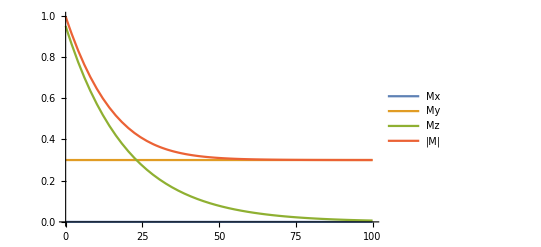

```mathematica
Clear[Bx,By,Bz,ωx,ωy,ωz,γ,T1,T2]
B={Bx,By,Bz};(*γBz = ωz is the Larmor frequency*)
mag0={0,0.3,0.95};
mag={Mx[t],My[t],Mz[t]};(*magnetization*)
Ω0=γ{{0,Bz,-By},{-Bz,0,Bx},{By,-Bx,0}}(*torque matrix with By=0. Bz(x) couples Mx-My (My-Mz)*)
Ωr=-γ{{0,Bz,0},{-Bz,0,0},{0,0,0}};(*going to a rotating frame = subtracting off the z bias field*)
γ=1;
(*Bz=ωz/γ;
Bx=ωx/γ;*)
Γ={{-1/T2,0,0},{-1/T2,0,0},{0,0,-1/T1}};(*decay matrix*)
magIC=Array[(mag/.t->0)[[#]]==mag0[[#]]&,3];
motionEqs=Thread[D[mag,t]==Dot[Ω+Ωr+Γ,mag]];
"Bloch equations:"
For[i=1,i<4,i++,
Print[motionEqs[[i]]//TraditionalForm]
]
Bz=1;
Bx=0*Cos[2π t];
By=0;
T1=20;(*demagnetization time. magnetization = sum of spin projections along z*)
T2=10;(*decoherence time. coherence = the relative phases of transverse spin components. this is decoherence*)
eqs=Flatten@Join[motionEqs,magIC];
tmax=100;
soln=First@NDSolve[eqs,mag,{t,0,tmax}];
{x,y,z}=Array[soln[[#,2]]&,3];
labels={"Mx","My","Mz","|M|"};
Plot[{x,y,z,Sqrt[x^2+y^2+z^2]},{t,0,tmax},PlotRange->All,PlotLegends->labels]
Manipulate[TorqueVectorSphere[{x,y,z}/.t->τ,B/(√(B.B))/.t->τ],{τ,0,tmax,0.001} ]
```